{2,4,8,16,32,5,10,20,40,21,42,25,50,41,23,46,33,7,14,28,56,53,47,35,11,22,44,29,58,57,55,51,43,27,54,49,39,19,38,17,34,9,18,36,13,26,52,45,31,3,6,12,24,48,37,15,30,1}

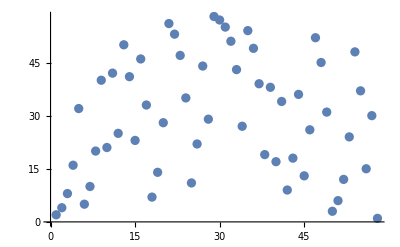

```mathematica
p=59;
l = PowerMod[2,Range[1,p-1],p]
ListPlot[l]
```

7919

{2,4,8,16,32,64,128,256,512,1024,2048,4096,273,546,1092,2184,4368,817,1634,3268,6536,5153,2387,4774,1629,3258,6516,5113,2307,4614,1309,2618,5236,2553,5106,2293,4586,1253,2506,5012,2105,4210,501,1002,2004,4008,97,194,388,776,1552,3104,6208,4497,1075,2150,4300,681,1362,2724,5448,2977,5954,3989,59,118,236,472,944,1888,3776,7552,7185,6451,4983,2047,4094,269,538,1076,2152,4304,689,1378,2756,5512,3105,6210,4501,1083,2166,4332,745,1490,2980,5960,4001,83,166,332,664,1328,2656,5312,2705,5410,2901,5802,3685,7370,6821,5723,3527,7054,6189,4459,999,1998,3996,73,146,292,584,1168,2336,4672,1425,2850,5700,3481,6962,6005,4091,263,526,1052,2104,4208,497,994,1988,3976,33,66,132,264,528,1056,2112,4224,529,1058,2116,4232,545,1090,2180,4360,801,1602,3204,6408,4897,1875,3750,7500,7081,6243,4567,1215,2430,4860,1801,3602,7204,6489,5059,2199,4398,877,1754,3508,7016,6113,4307,695,1390,2780,5560,3201,6402,4885,1851,3702,7404,6889,5859,3799,7598,7277,6635,5351,2783,5566,3213,6426,4933,1947,3894,7788,7657,7395,6871,5823,3727,7454,6989,6059,4199,479,958,1916,3832,7664,7409,6899,5879,3839,7678,7437,6955,5991,4063,207,414,828,1656,3312,6624,5329,2739,5478,3037,6074,4229,539,1078,2156,4312,705,1410,2820,5640,3361,6722,5525,3131,6262,4605,1291,2582,5164,2409,4818,1717,3434,6868,5817,3715,7430,6941,5963,4007,95,190,380,760,1520,3040,6080,4241,563,1126,2252,4504,1089,2178,4356,793,1586,3172,6344,4769,1619,3238,6476,5033,2147,4294,669,1338,2676,5352,2785,5570,3221,6442,4965,2011,4022,125,250,500,1000,2000,4000,81,162,324,648,1296,2592,5184,2449,4898,1877,3754,7508,7097,6275,4631,1343,2686,5372,2825,5650,3381,6762,5605,3291,6582,5245,2571,5142,2365,4730,1541,3082,6164,4409,899,1798,3596,7192,6465,5011,2103,4206,493,986,1972,3944,7888,7857,7795,7671,7423,6927,5935,3951,7902,7885,7851,7783,7647,7375,6831,5743,3567,7134,6349,4779,1639,3278,6556,5193,2467,4934,1949,3898,7796,7673,7427,6935,5951,3983,47,94,188,376,752,1504,3008,6016,4113,307,614,1228,2456,4912,1905,3810,7620,7321,6723,5527,3135,6270,4621,1323,2646,5292,2665,5330,2741,5482,3045,6090,4261,603,1206,2412,4824,1729,3458,6916,5913,3907,7814,7709,7499,7079,6239,4559,1199,2398,4796,1673,3346,6692,5465,3011,6022,4125,331,662,1324,2648,5296,2673,5346,2773,5546,3173,6346,4773,1627,3254,6508,5097,2275,4550,1181,2362,4724,1529,3058,6116,4313,707,1414,2828,5656,3393,6786,5653,3387,6774,5629,3339,6678,5437,2955,5910,3901,7802,7685,7451,6983,6047,4175,431,862,1724,3448,6896,5873,3827,7654,7389,6859,5799,3679,7358,6797,5675,3431,6862,5805,3691,7382,6845,5771,3623,7246,6573,5227,2535,5070,2221,4442,965,1930,3860,7720,7521,7123,6327,4735,1551,3102,6204,4489,1059,2118,4236,553,1106,2212,4424,929,1858,3716,7432,6945,5971,4023,127,254,508,1016,2032,4064,209,418,836,1672,3344,6688,5457,2995,5990,4061,203,406,812,1624,3248,6496,5073,2227,4454,989,1978,3956,7912,7905,7891,7863,7807,7695,7471,7023,6127,4335,751,1502,3004,6008,4097,275,550,1100,2200,4400,881,1762,3524,7048,6177,4435,951,1902,3804,7608,7297,6675,5431,2943,5886,3853,7706,7493,7067,6215,4511,1103,2206,4412,905,1810,3620,7240,6561,5203,2487,4974,2029,4058,197,394,788,1576,3152,6304,4689,1459,2918,5836,3753,7506,7093,6267,4615,1311,2622,5244,2569,5138,2357,4714,1509,3018,6036,4153,387,774,1548,3096,6192,4465,1011,2022,4044,169,338,676,1352,2704,5408,2897,5794,3669,7338,6757,5595,3271,6542,5165,2411,4822,1725,3450,6900,5881,3843,7686,7453,6987,6055,4191,463,926,1852,3704,7408,6897,5875,3831,7662,7405,6891,5863,3807,7614,7309,6699,5479,3039,6078,4237,555,1110,2220,4440,961,1922,3844,7688,7457,6995,6071,4223,527,1054,2108,4216,513,1026,2052,4104,289,578,1156,2312,4624,1329,2658,5316,2713,5426,2933,5866,3813,7626,7333,6747,5575,3231,6462,5005,2091,4182,445,890,1780,3560,7120,6321,4723,1527,3054,6108,4297,675,1350,2700,5400,2881,5762,3605,7210,6501,5083,2247,4494,1069,2138,4276,633,1266,2532,5064,2209,4418,917,1834,3668,7336,6753,5587,3255,6510,5101,2283,4566,1213,2426,4852,1785,3570,7140,6361,4803,1687,3374,6748,5577,3235,6470,5021,2123,4246,573,1146,2292,4584,1249,2498,4996,2073,4146,373,746,1492,2984,5968,4017,115,230,460,920,1840,3680,7360,6801,5683,3447,6894,5869,3819,7638,7357,6795,5671,3423,6846,5773,3627,7254,6589,5259,2599,5198,2477,4954,1989,3978,37,74,148,296,592,1184,2368,4736,1553,3106,6212,4505,1091,2182,4364,809,1618,3236,6472,5025,2131,4262,605,1210,2420,4840,1761,3522,7044,6169,4419,919,1838,3676,7352,6785,5651,3383,6766,5613,3307,6614,5309,2699,5398,2877,5754,3589,7178,6437,4955,1991,3982,45,90,180,360,720,1440,2880,5760,3601,7202,6485,5051,2183,4366,813,1626,3252,6504,5089,2259,4518,1117,2234,4468,1017,2034,4068,217,434,868,1736,3472,6944,5969,4019,119,238,476,952,1904,3808,7616,7313,6707,5495,3071,6142,4365,811,1622,3244,6488,5057,2195,4390,861,1722,3444,6888,5857,3795,7590,7261,6603,5287,2655,5310,2701,5402,2885,5770,3621,7242,6565,5211,2503,5006,2093,4186,453,906,1812,3624,7248,6577,5235,2551,5102,2285,4570,1221,2442,4884,1849,3698,7396,6873,5827,3735,7470,7021,6123,4327,735,1470,2940,5880,3841,7682,7445,6971,6023,4127,335,670,1340,2680,5360,2801,5602,3285,6570,5221,2523,5046,2173,4346,773,1546,3092,6184,4449,979,1958,3916,7832,7745,7571,7223,6527,5135,2351,4702,1485,2970,5940,3961,3,6,12,24,48,96,192,384,768,1536,3072,6144,4369,819,1638,3276,6552,5185,2451,4902,1885,3770,7540,7161,6403,4887,1855,3710,7420,6921,5923,3927,7854,7789,7659,7399,6879,5839,3759,7518,7117,6315,4711,1503,3006,6012,4105,291,582,1164,2328,4656,1393,2786,5572,3225,6450,4981,2043,4086,253,506,1012,2024,4048,177,354,708,1416,2832,5664,3409,6818,5717,3515,7030,6141,4363,807,1614,3228,6456,4993,2067,4134,349,698,1396,2792,5584,3249,6498,5077,2235,4470,1021,2042,4084,249,498,996,1992,3984,49,98,196,392,784,1568,3136,6272,4625,1331,2662,5324,2729,5458,2997,5994,4069,219,438,876,1752,3504,7008,6097,4275,631,1262,2524,5048,2177,4354,789,1578,3156,6312,4705,1491,2982,5964,4009,99,198,396,792,1584,3168,6336,4753,1587,3174,6348,4777,1635,3270,6540,5161,2403,4806,1693,3386,6772,5625,3331,6662,5405,2891,5782,3645,7290,6661,5403,2887,5774,3629,7258,6597,5275,2631,5262,2605,5210,2501,5002,2085,4170,421,842,1684,3368,6736,5553,3187,6374,4829,1739,3478,6956,5993,4067,215,430,860,1720,3440,6880,5841,3763,7526,7133,6347,4775,1631,3262,6524,5129,2339,4678,1437,2874,5748,3577,7154,6389,4859,1799,3598,7196,6473,5027,2135,4270,621,1242,2484,4968,2017,4034,149,298,596,1192,2384,4768,1617,3234,6468,5017,2115,4230,541,1082,2164,4328,737,1474,2948,5896,3873,7746,7573,7227,6535,5151,2383,4766,1613,3226,6452,4985,2051,4102,285,570,1140,2280,4560,1201,2402,4804,1689,3378,6756,5593,3267,6534,5149,2379,4758,1597,3194,6388,4857,1795,3590,7180,6441,4963,2007,4014,109,218,436,872,1744,3488,6976,6033,4147,375,750,1500,3000,6000,4081,243,486,972,1944,3888,7776,7633,7347,6775,5631,3343,6686,5453,2987,5974,4029,139,278,556,1112,2224,4448,977,1954,3908,7816,7713,7507,7095,6271,4623,1327,2654,5308,2697,5394,2869,5738,3557,7114,6309,4699,1479,2958,5916,3913,7826,7733,7547,7175,6431,4943,1967,3934,7868,7817,7715,7511,7103,6287,4655,1391,2782,5564,3209,6418,4917,1915,3830,7660,7401,6883,5847,3775,7550,7181,6443,4967,2015,4030,141,282,564,1128,2256,4512,1105,2210,4420,921,1842,3684,7368,6817,5715,3511,7022,6125,4331,743,1486,2972,5944,3969,19,38,76,152,304,608,1216,2432,4864,1809,3618,7236,6553,5187,2455,4910,1901,3802,7604,7289,6659,5399,2879,5758,3597,7194,6469,5019,2119,4238,557,1114,2228,4456,993,1986,3972,25,50,100,200,400,800,1600,3200,6400,4881,1843,3686,7372,6825,5731,3543,7086,6253,4587,1255,2510,5020,2121,4242,565,1130,2260,4520,1121,2242,4484,1049,2098,4196,473,946,1892,3784,7568,7217,6515,5111,2303,4606,1293,2586,5172,2425,4850,1781,3562,7124,6329,4739,1559,3118,6236,4553,1187,2374,4748,1577,3154,6308,4697,1475,2950,5900,3881,7762,7605,7291,6663,5407,2895,5790,3661,7322,6725,5531,3143,6286,4653,1387,2774,5548,3177,6354,4789,1659,3318,6636,5353,2787,5574,3229,6458,4997,2075,4150,381,762,1524,3048,6096,4273,627,1254,2508,5016,2113,4226,533,1066,2132,4264,609,1218,2436,4872,1825,3650,7300,6681,5443,2967,5934,3949,7898,7877,7835,7751,7583,7247,6575,5231,2543,5086,2253,4506,1093,2186,4372,825,1650,3300,6600,5281,2643,5286,2653,5306,2693,5386,2853,5706,3493,6986,6053,4187,455,910,1820,3640,7280,6641,5363,2807,5614,3309,6618,5317,2715,5430,2941,5882,3845,7690,7461,7003,6087,4255,591,1182,2364,4728,1537,3074,6148,4377,835,1670,3340,6680,5441,2963,5926,3933,7866,7813,7707,7495,7071,6223,4527,1135,2270,4540,1161,2322,4644,1369,2738,5476,3033,6066,4213,507,1014,2028,4056,193,386,772,1544,3088,6176,4433,947,1894,3788,7576,7233,6547,5175,2431,4862,1805,3610,7220,6521,5123,2327,4654,1389,2778,5556,3193,6386,4853,1787,3574,7148,6377,4835,1751,3502,7004,6089,4259,599,1198,2396,4792,1665,3330,6660,5401,2883,5766,3613,7226,6533,5147,2375,4750,1581,3162,6324,4729,1539,3078,6156,4393,867,1734,3468,6936,5953,3987,55,110,220,440,880,1760,3520,7040,6161,4403,887,1774,3548,7096,6273,4627,1335,2670,5340,2761,5522,3125,6250,4581,1243,2486,4972,2025,4050,181,362,724,1448,2896,5792,3665,7330,6741,5563,3207,6414,4909,1899,3798,7596,7273,6627,5335,2751,5502,3085,6170,4421,923,1846,3692,7384,6849,5779,3639,7278,6637,5355,2791,5582,3245,6490,5061,2203,4406,893,1786,3572,7144,6369,4819,1719,3438,6876,5833,3747,7494,7069,6219,4519,1119,2238,4476,1033,2066,4132,345,690,1380,2760,5520,3121,6242,4565,1211,2422,4844,1769,3538,7076,6233,4547,1175,2350,4700,1481,2962,5924,3929,7858,7797,7675,7431,6943,5967,4015,111,222,444,888,1776,3552,7104,6289,4659,1399,2798,5596,3273,6546,5173,2427,4854,1789,3578,7156,6393,4867,1815,3630,7260,6601,5283,2647,5294,2669,5338,2757,5514,3109,6218,4517,1115,2230,4460,1001,2002,4004,89,178,356,712,1424,2848,5696,3473,6946,5973,4027,135,270,540,1080,2160,4320,721,1442,2884,5768,3617,7234,6549,5179,2439,4878,1837,3674,7348,6777,5635,3351,6702,5485,3051,6102,4285,651,1302,2604,5208,2497,4994,2069,4138,357,714,1428,2856,5712,3505,7010,6101,4283,647,1294,2588,5176,2433,4866,1813,3626,7252,6585,5251,2583,5166,2413,4826,1733,3466,6932,5945,3971,23,46,92,184,368,736,1472,2944,5888,3857,7714,7509,7099,6279,4639,1359,2718,5436,2953,5906,3893,7786,7653,7387,6855,5791,3663,7326,6733,5547,3175,6350,4781,1643,3286,6572,5225,2531,5062,2205,4410,901,1802,3604,7208,6497,5075,2231,4462,1005,2010,4020,121,242,484,968,1936,3872,7744,7569,7219,6519,5119,2319,4638,1357,2714,5428,2937,5874,3829,7658,7397,6875,5831,3743,7486,7053,6187,4455,991,1982,3964,9,18,36,72,144,288,576,1152,2304,4608,1297,2594,5188,2457,4914,1909,3818,7636,7353,6787,5655,3391,6782,5645,3371,6742,5565,3211,6422,4925,1931,3862,7724,7529,7139,6359,4799,1679,3358,6716,5513,3107,6214,4509,1099,2198,4396,873,1746,3492,6984,6049,4179,439,878,1756,3512,7024,6129,4339,759,1518,3036,6072,4225,531,1062,2124,4248,577,1154,2308,4616,1313,2626,5252,2585,5170,2421,4842,1765,3530,7060,6201,4483,1047,2094,4188,457,914,1828,3656,7312,6705,5491,3063,6126,4333,747,1494,2988,5976,4033,147,294,588,1176,2352,4704,1489,2978,5956,3993,67,134,268,536,1072,2144,4288,657,1314,2628,5256,2593,5186,2453,4906,1893,3786,7572,7225,6531,5143,2367,4734,1549,3098,6196,4473,1027,2054,4108,297,594,1188,2376,4752,1585,3170,6340,4761,1603,3206,6412,4905,1891,3782,7564,7209,6499,5079,2239,4478,1037,2074,4148,377,754,1508,3016,6032,4145,371,742,1484,2968,5936,3953,7906,7893,7867,7815,7711,7503,7087,6255,4591,1263,2526,5052,2185,4370,821,1642,3284,6568,5217,2515,5030,2141,4282,645,1290,2580,5160,2401,4802,1685,3370,6740,5561,3203,6406,4893,1867,3734,7468,7017,6115,4311,703,1406,2812,5624,3329,6658,5397,2875,5750,3581,7162,6405,4891,1863,3726,7452,6985,6051,4183,447,894,1788,3576,7152,6385,4851,1783,3566,7132,6345,4771,1623,3246,6492,5065,2211,4422,925,1850,3700,7400,6881,5843,3767,7534,7149,6379,4839,1759,3518,7036,6153,4387,855,1710,3420,6840,5761,3603,7206,6493,5067,2215,4430,941,1882,3764,7528,7137,6355,4791,1663,3326,6652,5385,2851,5702,3485,6970,6021,4123,327,654,1308,2616,5232,2545,5090,2261,4522,1125,2250,4500,1081,2162,4324,729,1458,2916,5832,3745,7490,7061,6203,4487,1055,2110,4220,521,1042,2084,4168,417,834,1668,3336,6672,5425,2931,5862,3805,7610,7301,6683,5447,2975,5950,3981,43,86,172,344,688,1376,2752,5504,3089,6178,4437,955,1910,3820,7640,7361,6803,5687,3455,6910,5901,3883,7766,7613,7307,6695,5471,3023,6046,4173,427,854,1708,3416,6832,5745,3571,7142,6365,4811,1703,3406,6812,5705,3491,6982,6045,4171,423,846,1692,3384,6768,5617,3315,6630,5341,2763,5526,3133,6266,4613,1307,2614,5228,2537,5074,2229,4458,997,1994,3988,57,114,228,456,912,1824,3648,7296,6673,5427,2935,5870,3821,7642,7365,6811,5703,3487,6974,6029,4139,359,718,1436,2872,5744,3569,7138,6357,4795,1671,3342,6684,5449,2979,5958,3997,75,150,300,600,1200,2400,4800,1681,3362,6724,5529,3139,6278,4637,1355,2710,5420,2921,5842,3765,7530,7141,6363,4807,1695,3390,6780,5641,3363,6726,5533,3147,6294,4669,1419,2838,5676,3433,6866,5813,3707,7414,6909,5899,3879,7758,7597,7275,6631,5343,2767,5534,3149,6298,4677,1435,2870,5740,3561,7122,6325,4731,1543,3086,6172,4425,931,1862,3724,7448,6977,6035,4151,383,766,1532,3064,6128,4337,755,1510,3020,6040,4161,403,806,1612,3224,6448,4977,2035,4070,221,442,884,1768,3536,7072,6225,4531,1143,2286,4572,1225,2450,4900,1881,3762,7524,7129,6339,4759,1599,3198,6396,4873,1827,3654,7308,6697,5475,3031,6062,4205,491,982,1964,3928,7856,7793,7667,7415,6911,5903,3887,7774,7629,7339,6759,5599,3279,6558,5197,2475,4950,1981,3962,5,10,20,40,80,160,320,640,1280,2560,5120,2321,4642,1365,2730,5460,3001,6002,4085,251,502,1004,2008,4016,113,226,452,904,1808,3616,7232,6545,5171,2423,4846,1773,3546,7092,6265,4611,1303,2606,5212,2505,5010,2101,4202,485,970,1940,3880,7760,7601,7283,6647,5375,2831,5662,3405,6810,5701,3483,6966,6013,4107,295,590,1180,2360,4720,1521,3042,6084,4249,579,1158,2316,4632,1345,2690,5380,2841,5682,3445,6890,5861,3803,7606,7293,6667,5415,2911,5822,3725,7450,6981,6043,4167,415,830,1660,3320,6640,5361,2803,5606,3293,6586,5253,2587,5174,2429,4858,1797,3594,7188,6457,4995,2071,4142,365,730,1460,2920,5840,3761,7522,7125,6331,4743,1567,3134,6268,4617,1315,2630,5260,2601,5202,2485,4970,2021,4042,165,330,660,1320,2640,5280,2641,5282,2645,5290,2661,5322,2725,5450,2981,5962,4005,91,182,364,728,1456,2912,5824,3729,7458,6997,6075,4231,543,1086,2172,4344,769,1538,3076,6152,4385,851,1702,3404,6808,5697,3475,6950,5981,4043,167,334,668,1336,2672,5344,2769,5538,3157,6314,4709,1499,2998,5996,4073,227,454,908,1816,3632,7264,6609,5299,2679,5358,2797,5594,3269,6538,5157,2395,4790,1661,3322,6644,5369,2819,5638,3357,6714,5509,3099,6198,4477,1035,2070,4140,361,722,1444,2888,5776,3633,7266,6613,5307,2695,5390,2861,5722,3525,7050,6181,4443,967,1934,3868,7736,7553,7187,6455,4991,2063,4126,333,666,1332,2664,5328,2737,5474,3029,6058,4197,475,950,1900,3800,7600,7281,6643,5367,2815,5630,3341,6682,5445,2971,5942,3965,11,22,44,88,176,352,704,1408,2816,5632,3345,6690,5461,3003,6006,4093,267,534,1068,2136,4272,625,1250,2500,5000,2081,4162,405,810,1620,3240,6480,5041,2163,4326,733,1466,2932,5864,3809,7618,7317,6715,5511,3103,6206,4493,1067,2134,4268,617,1234,2468,4936,1953,3906,7812,7705,7491,7063,6207,4495,1071,2142,4284,649,1298,2596,5192,2465,4930,1941,3882,7764,7609,7299,6679,5439,2959,5918,3917,7834,7749,7579,7239,6559,5199,2479,4958,1997,3994,69,138,276,552,1104,2208,4416,913,1826,3652,7304,6689,5459,2999,5998,4077,235,470,940,1880,3760,7520,7121,6323,4727,1535,3070,6140,4361,803,1606,3212,6424,4929,1939,3878,7756,7593,7267,6615,5311,2703,5406,2893,5786,3653,7306,6693,5467,3015,6030,4141,363,726,1452,2904,5808,3697,7394,6869,5819,3719,7438,6957,5995,4071,223,446,892,1784,3568,7136,6353,4787,1655,3310,6620,5321,2723,5446,2973,5946,3973,27,54,108,216,432,864,1728,3456,6912,5905,3891,7782,7645,7371,6823,5727,3535,7070,6221,4523,1127,2254,4508,1097,2194,4388,857,1714,3428,6856,5793,3667,7334,6749,5579,3239,6478,5037,2155,4310,701,1402,2804,5608,3297,6594,5269,2619,5238,2557,5114,2309,4618,1317,2634,5268,2617,5234,2549,5098,2277,4554,1189,2378,4756,1593,3186,6372,4825,1731,3462,6924,5929,3939,7878,7837,7755,7591,7263,6607,5295,2671,5342,2765,5530,3141,6282,4645,1371,2742,5484,3049,6098,4277,635,1270,2540,5080,2241,4482,1045,2090,4180,441,882,1764,3528,7056,6193,4467,1015,2030,4060,201,402,804,1608,3216,6432,4945,1971,3942,7884,7849,7779,7639,7359,6799,5679,3439,6878,5837,3755,7510,7101,6283,4647,1375,2750,5500,3081,6162,4405,891,1782,3564,7128,6337,4755,1591,3182,6364,4809,1699,3398,6796,5673,3427,6854,5789,3659,7318,6717,5515,3111,6222,4525,1131,2262,4524,1129,2258,4516,1113,2226,4452,985,1970,3940,7880,7841,7763,7607,7295,6671,5423,2927,5854,3789,7578,7237,6555,5191,2463,4926,1933,3866,7732,7545,7171,6423,4927,1935,3870,7740,7561,7203,6487,5055,2191,4382,845,1690,3380,6760,5601,3283,6566,5213,2507,5014,2109,4218,517,1034,2068,4136,353,706,1412,2824,5648,3377,6754,5589,3259,6518,5117,2315,4630,1341,2682,5364,2809,5618,3317,6634,5349,2779,5558,3197,6394,4869,1819,3638,7276,6633,5347,2775,5550,3181,6362,4805,1691,3382,6764,5609,3299,6598,5277,2635,5270,2621,5242,2565,5130,2341,4682,1445,2890,5780,3641,7282,6645,5371,2823,5646,3373,6746,5573,3227,6454,4989,2059,4118,317,634,1268,2536,5072,2225,4450,981,1962,3924,7848,7777,7635,7351,6783,5647,3375,6750,5581,3243,6486,5053,2187,4374,829,1658,3316,6632,5345,2771,5542,3165,6330,4741,1563,3126,6252,4585,1251,2502,5004,2089,4178,437,874,1748,3496,6992,6065,4211,503,1006,2012,4024,129,258,516,1032,2064,4128,337,674,1348,2696,5392,2865,5730,3541,7082,6245,4571,1223,2446,4892,1865,3730,7460,7001,6083,4247,575,1150,2300,4600,1281,2562,5124,2329,4658,1397,2794,5588,3257,6514,5109,2299,4598,1277,2554,5108,2297,4594,1269,2538,5076,2233,4466,1013,2026,4052,185,370,740,1480,2960,5920,3921,7842,7765,7611,7303,6687,5455,2991,5982,4045,171,342,684,1368,2736,5472,3025,6050,4181,443,886,1772,3544,7088,6257,4595,1271,2542,5084,2249,4498,1077,2154,4308,697,1394,2788,5576,3233,6466,5013,2107,4214,509,1018,2036,4072,225,450,900,1800,3600,7200,6481,5043,2167,4334,749,1498,2996,5992,4065,211,422,844,1688,3376,6752,5585,3251,6502,5085,2251,4502,1085,2170,4340,761,1522,3044,6088,4257,595,1190,2380,4760,1601,3202,6404,4889,1859,3718,7436,6953,5987,4055,191,382,764,1528,3056,6112,4305,691,1382,2764,5528,3137,6274,4629,1339,2678,5356,2793,5586,3253,6506,5093,2267,4534,1149,2298,4596,1273,2546,5092,2265,4530,1141,2282,4564,1209,2418,4836,1753,3506,7012,6105,4291,663,1326,2652,5304,2689,5378,2837,5674,3429,6858,5797,3675,7350,6781,5643,3367,6734,5549,3179,6358,4797,1675,3350,6700,5481,3043,6086,4253,587,1174,2348,4696,1473,2946,5892,3865,7730,7541,7163,6407,4895,1871,3742,7484,7049,6179,4439,959,1918,3836,7672,7425,6931,5943,3967,15,30,60,120,240,480,960,1920,3840,7680,7441,6963,6007,4095,271,542,1084,2168,4336,753,1506,3012,6024,4129,339,678,1356,2712,5424,2929,5858,3797,7594,7269,6619,5319,2719,5438,2957,5914,3909,7818,7717,7515,7111,6303,4687,1455,2910,5820,3721,7442,6965,6011,4103,287,574,1148,2296,4592,1265,2530,5060,2201,4402,885,1770,3540,7080,6241,4563,1207,2414,4828,1737,3474,6948,5977,4035,151,302,604,1208,2416,4832,1745,3490,6980,6041,4163,407,814,1628,3256,6512,5105,2291,4582,1245,2490,4980,2041,4082,245,490,980,1960,3920,7840,7761,7603,7287,6655,5391,2863,5726,3533,7066,6213,4507,1095,2190,4380,841,1682,3364,6728,5537,3155,6310,4701,1483,2966,5932,3945,7890,7861,7803,7687,7455,6991,6063,4207,495,990,1980,3960,1,2,4,8,16,32,64,128,256,512,1024,2048,4096,273,546,1092,2184,4368,817,1634,3268,6536,5153,2387,4774,1629,3258,6516,5113,2307,4614,1309,2618,5236,2553,5106,2293,4586,1253,2506,5012,2105,4210,501,1002,2004,4008,97,194,388,776,1552,3104,6208,4497,1075,2150,4300,681,1362,2724,5448,2977,5954,3989,59,118,236,472,944,1888,3776,7552,7185,6451,4983,2047,4094,269,538,1076,2152,4304,689,1378,2756,5512,3105,6210,4501,1083,2166,4332,745,1490,2980,5960,4001,83,166,332,664,1328,2656,5312,2705,5410,2901,5802,3685,7370,6821,5723,3527,7054,6189,4459,999,1998,3996,73,146,292,584,1168,2336,4672,1425,2850,5700,3481,6962,6005,4091,263,526,1052,2104,4208,497,994,1988,3976,33,66,132,264,528,1056,2112,4224,529,1058,2116,4232,545,1090,2180,4360,801,1602,3204,6408,4897,1875,3750,7500,7081,6243,4567,1215,2430,4860,1801,3602,7204,6489,5059,2199,4398,877,1754,3508,7016,6113,4307,695,1390,2780,5560,3201,6402,4885,1851,3702,7404,6889,5859,3799,7598,7277,6635,5351,2783,5566,3213,6426,4933,1947,3894,7788,7657,7395,6871,5823,3727,7454,6989,6059,4199,479,958,1916,3832,7664,7409,6899,5879,3839,7678,7437,6955,5991,4063,207,414,828,1656,3312,6624,5329,2739,5478,3037,6074,4229,539,1078,2156,4312,705,1410,2820,5640,3361,6722,5525,3131,6262,4605,1291,2582,5164,2409,4818,1717,3434,6868,5817,3715,7430,6941,5963,4007,95,190,380,760,1520,3040,6080,4241,563,1126,2252,4504,1089,2178,4356,793,1586,3172,6344,4769,1619,3238,6476,5033,2147,4294,669,1338,2676,5352,2785,5570,3221,6442,4965,2011,4022,125,250,500,1000,2000,4000,81,162,324,648,1296,2592,5184,2449,4898,1877,3754,7508,7097,6275,4631,1343,2686,5372,2825,5650,3381,6762,5605,3291,6582,5245,2571,5142,2365,4730,1541,3082,6164,4409,899,1798,3596,7192,6465,5011,2103,4206,493,986,1972,3944,7888,7857,7795,7671,7423,6927,5935,3951,7902,7885,7851,7783,7647,7375,6831,5743,3567,7134,6349,4779,1639,3278,6556,5193,2467,4934,1949,3898,7796,7673,7427,6935,5951,3983,47,94,188,376,752,1504,3008,6016,4113,307,614,1228,2456,4912,1905,3810,7620,7321,6723,5527,3135,6270,4621,1323,2646,5292,2665,5330,2741,5482,3045,6090,4261,603,1206,2412,4824,1729,3458,6916,5913,3907,7814,7709,7499,7079,6239,4559,1199,2398,4796,1673,3346,6692,5465,3011,6022,4125,331,662,1324,2648,5296,2673,5346,2773,5546,3173,6346,4773,1627,3254,6508,5097,2275,4550,1181,2362,4724,1529,3058,6116,4313,707,1414,2828,5656,3393,6786,5653,3387,6774,5629,3339,6678,5437,2955,5910,3901,7802,7685,7451,6983,6047,4175,431,862,1724,3448,6896,5873,3827,7654,7389,6859,5799,3679,7358,6797,5675,3431,6862,5805,3691,7382,6845,5771,3623,7246,6573,5227,2535,5070,2221,4442,965,1930,3860,7720,7521,7123,6327,4735,1551,3102,6204,4489,1059,2118,4236,553,1106,2212,4424,929,1858,3716,7432,6945,5971,4023,127,254,508,1016,2032,4064,209,418,836,1672,3344,6688,5457,2995,5990,4061,203,406,812,1624,3248,6496,5073,2227,4454,989,1978,3956,7912,7905,7891,7863,7807,7695,7471,7023,6127,4335,751,1502,3004,6008,4097,275,550,1100,2200,4400,881,1762,3524,7048,6177,4435,951,1902,3804,7608,7297,6675,5431,2943,5886,3853,7706,7493,7067,6215,4511,1103,2206,4412,905,1810,3620,7240,6561,5203,2487,4974,2029,4058,197,394,788,1576,3152,6304,4689,1459,2918,5836,3753,7506,7093,6267,4615,1311,2622,5244,2569,5138,2357,4714,1509,3018,6036,4153,387,774,1548,3096,6192,4465,1011,2022,4044,169,338,676,1352,2704,5408,2897,5794,3669,7338,6757,5595,3271,6542,5165,2411,4822,1725,3450,6900,5881,3843,7686,7453,6987,6055,4191,463,926,1852,3704,7408,6897,5875,3831,7662,7405,6891,5863,3807,7614,7309,6699,5479,3039,6078,4237,555,1110,2220,4440,961,1922,3844,7688,7457,6995,6071,4223,527,1054,2108,4216,513,1026,2052,4104,289,578,1156,2312,4624,1329,2658,5316,2713,5426,2933,5866,3813,7626,7333,6747,5575,3231,6462,5005,2091,4182,445,890,1780,3560,7120,6321,4723,1527,3054,6108,4297,675,1350,2700,5400,2881,5762,3605,7210,6501,5083,2247,4494,1069,2138,4276,633,1266,2532,5064,2209,4418,917,1834,3668,7336,6753,5587,3255,6510,5101,2283,4566,1213,2426,4852,1785,3570,7140,6361,4803,1687,3374,6748,5577,3235,6470,5021,2123,4246,573,1146,2292,4584,1249,2498,4996,2073,4146,373,746,1492,2984,5968,4017,115,230,460,920,1840,3680,7360,6801,5683,3447,6894,5869,3819,7638,7357,6795,5671,3423,6846,5773,3627,7254,6589,5259,2599,5198,2477,4954,1989,3978,37,74,148,296,592,1184,2368,4736,1553,3106,6212,4505,1091,2182,4364,809,1618,3236,6472,5025,2131,4262,605,1210,2420,4840,1761,3522,7044,6169,4419,919,1838,3676,7352,6785,5651,3383,6766,5613,3307,6614,5309,2699,5398,2877,5754,3589,7178,6437,4955,1991,3982,45,90,180,360,720,1440,2880,5760,3601,7202,6485,5051,2183,4366,813,1626,3252,6504,5089,2259,4518,1117,2234,4468,1017,2034,4068,217,434,868,1736,3472,6944,5969,4019,119,238,476,952,1904,3808,7616,7313,6707,5495,3071,6142,4365,811,1622,3244,6488,5057,2195,4390,861,1722,3444,6888,5857,3795,7590,7261,6603,5287,2655,5310,2701,5402,2885,5770,3621,7242,6565,5211,2503,5006,2093,4186,453,906,1812,3624,7248,6577,5235,2551,5102,2285,4570,1221,2442,4884,1849,3698,7396,6873,5827,3735,7470,7021,6123,4327,735,1470,2940,5880,3841,7682,7445,6971,6023,4127,335,670,1340,2680,5360,2801,5602,3285,6570,5221,2523,5046,2173,4346,773,1546,3092,6184,4449,979,1958,3916,7832,7745,7571,7223,6527,5135,2351,4702,1485,2970,5940,3961,3,6,12,24,48,96,192,384,768,1536,3072,6144,4369,819,1638,3276,6552,5185,2451,4902,1885,3770,7540,7161,6403,4887,1855,3710,7420,6921,5923,3927,7854,7789,7659,7399,6879,5839,3759,7518,7117,6315,4711,1503,3006,6012,4105,291,582,1164,2328,4656,1393,2786,5572,3225,6450,4981,2043,4086,253,506,1012,2024,4048,177,354,708,1416,2832,5664,3409,6818,5717,3515,7030,6141,4363,807,1614,3228,6456,4993,2067,4134,349,698,1396,2792,5584,3249,6498,5077,2235,4470,1021,2042,4084,249,498,996,1992,3984,49,98,196,392,784,1568,3136,6272,4625,1331,2662,5324,2729,5458,2997,5994,4069,219,438,876,1752,3504,7008,6097,4275,631,1262,2524,5048,2177,4354,789,1578,3156,6312,4705,1491,2982,5964,4009,99,198,396,792,1584,3168,6336,4753,1587,3174,6348,4777,1635,3270,6540,5161,2403,4806,1693,3386,6772,5625,3331,6662,5405,2891,5782,3645,7290,6661,5403,2887,5774,3629,7258,6597,5275,2631,5262,2605,5210,2501,5002,2085,4170,421,842,1684,3368,6736,5553,3187,6374,4829,1739,3478,6956,5993,4067,215,430,860,1720,3440,6880,5841,3763,7526,7133,6347,4775,1631,3262,6524,5129,2339,4678,1437,2874,5748,3577,7154,6389,4859,1799,3598,7196,6473,5027,2135,4270,621,1242,2484,4968,2017,4034,149,298,596,1192,2384,4768,1617,3234,6468,5017,2115,4230,541,1082,2164,4328,737,1474,2948,5896,3873,7746,7573,7227,6535,5151,2383,4766,1613,3226,6452,4985,2051,4102,285,570,1140,2280,4560,1201,2402,4804,1689,3378,6756,5593,3267,6534,5149,2379,4758,1597,3194,6388,4857,1795,3590,7180,6441,4963,2007,4014,109,218,436,872,1744,3488,6976,6033,4147,375,750,1500,3000,6000,4081,243,486,972,1944,3888,7776,7633,7347,6775,5631,3343,6686,5453,2987,5974,4029,139,278,556,1112,2224,4448,977,1954,3908,7816,7713,7507,7095,6271,4623,1327,2654,5308,2697,5394,2869,5738,3557,7114,6309,4699,1479,2958,5916,3913,7826,7733,7547,7175,6431,4943,1967,3934,7868,7817,7715,7511,7103,6287,4655,1391,2782,5564,3209,6418,4917,1915,3830,7660,7401,6883,5847,3775,7550,7181,6443,4967,2015,4030,141,282,564,1128,2256,4512,1105,2210,4420,921,1842,3684,7368,6817,5715,3511,7022,6125,4331,743,1486,2972,5944,3969,19,38,76,152,304,608,1216,2432,4864,1809,3618,7236,6553,5187,2455,4910,1901,3802,7604,7289,6659,5399,2879,5758,3597,7194,6469,5019,2119,4238,557,1114,2228,4456,993,1986,3972,25,50,100,200,400,800,1600,3200,6400,4881,1843,3686,7372,6825,5731,3543,7086,6253,4587,1255,2510,5020,2121,4242,565,1130,2260,4520,1121,2242,4484,1049,2098,4196,473,946,1892,3784,7568,7217,6515,5111,2303,4606,1293,2586,5172,2425,4850,1781,3562,7124,6329,4739,1559,3118,6236,4553,1187,2374,4748,1577,3154,6308,4697,1475,2950,5900,3881,7762,7605,7291,6663,5407,2895,5790,3661,7322,6725,5531,3143,6286,4653,1387,2774,5548,3177,6354,4789,1659,3318,6636,5353,2787,5574,3229,6458,4997,2075,4150,381,762,1524,3048,6096,4273,627,1254,2508,5016,2113,4226,533,1066,2132,4264,609,1218,2436,4872,1825,3650,7300,6681,5443,2967,5934,3949,7898,7877,7835,7751,7583,7247,6575,5231,2543,5086,2253,4506,1093,2186,4372,825,1650,3300,6600,5281,2643,5286,2653,5306,2693,5386,2853,5706,3493,6986,6053,4187,455,910,1820,3640,7280,6641,5363,2807,5614,3309,6618,5317,2715,5430,2941,5882,3845,7690,7461,7003,6087,4255,591,1182,2364,4728,1537,3074,6148,4377,835,1670,3340,6680,5441,2963,5926,3933,7866,7813,7707,7495,7071,6223,4527,1135,2270,4540,1161,2322,4644,1369,2738,5476,3033,6066,4213,507,1014,2028,4056,193,386,772,1544,3088,6176,4433,947,1894,3788,7576,7233,6547,5175,2431,4862,1805,3610,7220,6521,5123,2327,4654,1389,2778,5556,3193,6386,4853,1787,3574,7148,6377,4835,1751,3502,7004,6089,4259,599,1198,2396,4792,1665,3330,6660,5401,2883,5766,3613,7226,6533,5147,2375,4750,1581,3162,6324,4729,1539,3078,6156,4393,867,1734,3468,6936,5953,3987,55,110,220,440,880,1760,3520,7040,6161,4403,887,1774,3548,7096,6273,4627,1335,2670,5340,2761,5522,3125,6250,4581,1243,2486,4972,2025,4050,181,362,724,1448,2896,5792,3665,7330,6741,5563,3207,6414,4909,1899,3798,7596,7273,6627,5335,2751,5502,3085,6170,4421,923,1846,3692,7384,6849,5779,3639,7278,6637,5355,2791,5582,3245,6490,5061,2203,4406,893,1786,3572,7144,6369,4819,1719,3438,6876,5833,3747,7494,7069,6219,4519,1119,2238,4476,1033,2066,4132,345,690,1380,2760,5520,3121,6242,4565,1211,2422,4844,1769,3538,7076,6233,4547,1175,2350,4700,1481,2962,5924,3929,7858,7797,7675,7431,6943,5967,4015,111,222,444,888,1776,3552,7104,6289,4659,1399,2798,5596,3273,6546,5173,2427,4854,1789,3578,7156,6393,4867,1815,3630,7260,6601,5283,2647,5294,2669,5338,2757,5514,3109,6218,4517,1115,2230,4460,1001,2002,4004,89,178,356,712,1424,2848,5696,3473,6946,5973,4027,135,270,540,1080,2160,4320,721,1442,2884,5768,3617,7234,6549,5179,2439,4878,1837,3674,7348,6777,5635,3351,6702,5485,3051,6102,4285,651,1302,2604,5208,2497,4994,2069,4138,357,714,1428,2856,5712,3505,7010,6101,4283,647,1294,2588,5176,2433,4866,1813,3626,7252,6585,5251,2583,5166,2413,4826,1733,3466,6932,5945,3971,23,46,92,184,368,736,1472,2944,5888,3857,7714,7509,7099,6279,4639,1359,2718,5436,2953,5906,3893,7786,7653,7387,6855,5791,3663,7326,6733,5547,3175,6350,4781,1643,3286,6572,5225,2531,5062,2205,4410,901,1802,3604,7208,6497,5075,2231,4462,1005,2010,4020,121,242,484,968,1936,3872,7744,7569,7219,6519,5119,2319,4638,1357,2714,5428,2937,5874,3829,7658,7397,6875,5831,3743,7486,7053,6187,4455,991,1982,3964,9,18,36,72,144,288,576,1152,2304,4608,1297,2594,5188,2457,4914,1909,3818,7636,7353,6787,5655,3391,6782,5645,3371,6742,5565,3211,6422,4925,1931,3862,7724,7529,7139,6359,4799,1679,3358,6716,5513,3107,6214,4509,1099,2198,4396,873,1746,3492,6984,6049,4179,439,878,1756,3512,7024,6129,4339,759,1518,3036,6072,4225,531,1062,2124,4248,577,1154,2308,4616,1313,2626,5252,2585,5170,2421,4842,1765,3530,7060,6201,4483,1047,2094,4188,457,914,1828,3656,7312,6705,5491,3063,6126,4333,747,1494,2988,5976,4033,147,294,588,1176,2352,4704,1489,2978,5956,3993,67,134,268,536,1072,2144,4288,657,1314,2628,5256,2593,5186,2453,4906,1893,3786,7572,7225,6531,5143,2367,4734,1549,3098,6196,4473,1027,2054,4108,297,594,1188,2376,4752,1585,3170,6340,4761,1603,3206,6412,4905,1891,3782,7564,7209,6499,5079,2239,4478,1037,2074,4148,377,754,1508,3016,6032,4145,371,742,1484,2968,5936,3953,7906,7893,7867,7815,7711,7503,7087,6255,4591,1263,2526,5052,2185,4370,821,1642,3284,6568,5217,2515,5030,2141,4282,645,1290,2580,5160,2401,4802,1685,3370,6740,5561,3203,6406,4893,1867,3734,7468,7017,6115,4311,703,1406,2812,5624,3329,6658,5397,2875,5750,3581,7162,6405,4891,1863,3726,7452,6985,6051,4183,447,894,1788,3576,7152,6385,4851,1783,3566,7132,6345,4771,1623,3246,6492,5065,2211,4422,925,1850,3700,7400,6881,5843,3767,7534,7149,6379,4839,1759,3518,7036,6153,4387,855,1710,3420,6840,5761,3603,7206,6493,5067,2215,4430,941,1882,3764,7528,7137,6355,4791,1663,3326,6652,5385,2851,5702,3485,6970,6021,4123,327,654,1308,2616,5232,2545,5090,2261,4522,1125,2250,4500,1081,2162,4324,729,1458,2916,5832,3745,7490,7061,6203,4487,1055,2110,4220,521,1042,2084,4168,417,834,1668,3336,6672,5425,2931,5862,3805,7610,7301,6683,5447,2975,5950,3981,43,86,172,344,688,1376,2752,5504,3089,6178,4437,955,1910,3820,7640,7361,6803,5687,3455,6910,5901,3883,7766,7613,7307,6695,5471,3023,6046,4173,427,854,1708,3416,6832,5745,3571,7142,6365,4811,1703,3406,6812,5705,3491,6982,6045,4171,423,846,1692,3384,6768,5617,3315,6630,5341,2763,5526,3133,6266,4613,1307,2614,5228,2537,5074,2229,4458,997,1994,3988,57,114,228,456,912,1824,3648,7296,6673,5427,2935,5870,3821,7642,7365,6811,5703,3487,6974,6029,4139,359,718,1436,2872,5744,3569,7138,6357,4795,1671,3342,6684,5449,2979,5958,3997,75,150,300,600,1200,2400,4800,1681,3362,6724,5529,3139,6278,4637,1355,2710,5420,2921,5842,3765,7530,7141,6363,4807,1695,3390,6780,5641,3363,6726,5533,3147,6294,4669,1419,2838,5676,3433,6866,5813,3707,7414,6909,5899,3879,7758,7597,7275,6631,5343,2767,5534,3149,6298,4677,1435,2870,5740,3561,7122,6325,4731,1543,3086,6172,4425,931,1862,3724,7448,6977,6035,4151,383,766,1532,3064,6128,4337,755,1510,3020,6040,4161,403,806,1612,3224,6448,4977,2035,4070,221,442,884,1768,3536,7072,6225,4531,1143,2286,4572,1225,2450,4900,1881,3762,7524,7129,6339,4759,1599,3198,6396,4873,1827,3654,7308,6697,5475,3031,6062,4205,491,982,1964,3928,7856,7793,7667,7415,6911,5903,3887,7774,7629,7339,6759,5599,3279,6558,5197,2475,4950,1981,3962,5,10,20,40,80,160,320,640,1280,2560,5120,2321,4642,1365,2730,5460,3001,6002,4085,251,502,1004,2008,4016,113,226,452,904,1808,3616,7232,6545,5171,2423,4846,1773,3546,7092,6265,4611,1303,2606,5212,2505,5010,2101,4202,485,970,1940,3880,7760,7601,7283,6647,5375,2831,5662,3405,6810,5701,3483,6966,6013,4107,295,590,1180,2360,4720,1521,3042,6084,4249,579,1158,2316,4632,1345,2690,5380,2841,5682,3445,6890,5861,3803,7606,7293,6667,5415,2911,5822,3725,7450,6981,6043,4167,415,830,1660,3320,6640,5361,2803,5606,3293,6586,5253,2587,5174,2429,4858,1797,3594,7188,6457,4995,2071,4142,365,730,1460,2920,5840,3761,7522,7125,6331,4743,1567,3134,6268,4617,1315,2630,5260,2601,5202,2485,4970,2021,4042,165,330,660,1320,2640,5280,2641,5282,2645,5290,2661,5322,2725,5450,2981,5962,4005,91,182,364,728,1456,2912,5824,3729,7458,6997,6075,4231,543,1086,2172,4344,769,1538,3076,6152,4385,851,1702,3404,6808,5697,3475,6950,5981,4043,167,334,668,1336,2672,5344,2769,5538,3157,6314,4709,1499,2998,5996,4073,227,454,908,1816,3632,7264,6609,5299,2679,5358,2797,5594,3269,6538,5157,2395,4790,1661,3322,6644,5369,2819,5638,3357,6714,5509,3099,6198,4477,1035,2070,4140,361,722,1444,2888,5776,3633,7266,6613,5307,2695,5390,2861,5722,3525,7050,6181,4443,967,1934,3868,7736,7553,7187,6455,4991,2063,4126,333,666,1332,2664,5328,2737,5474,3029,6058,4197,475,950,1900,3800,7600,7281,6643,5367,2815,5630,3341,6682,5445,2971,5942,3965,11,22,44,88,176,352,704,1408,2816,5632,3345,6690,5461,3003,6006,4093,267,534,1068,2136,4272,625,1250,2500,5000,2081,4162,405,810,1620,3240,6480,5041,2163,4326,733,1466,2932,5864,3809,7618,7317,6715,5511,3103,6206,4493,1067,2134,4268,617,1234,2468,4936,1953,3906,7812,7705,7491,7063,6207,4495,1071,2142,4284,649,1298,2596,5192,2465,4930,1941,3882,7764,7609,7299,6679,5439,2959,5918,3917,7834,7749,7579,7239,6559,5199,2479,4958,1997,3994,69,138,276,552,1104,2208,4416,913,1826,3652,7304,6689,5459,2999,5998,4077,235,470,940,1880,3760,7520,7121,6323,4727,1535,3070,6140,4361,803,1606,3212,6424,4929,1939,3878,7756,7593,7267,6615,5311,2703,5406,2893,5786,3653,7306,6693,5467,3015,6030,4141,363,726,1452,2904,5808,3697,7394,6869,5819,3719,7438,6957,5995,4071,223,446,892,1784,3568,7136,6353,4787,1655,3310,6620,5321,2723,5446,2973,5946,3973,27,54,108,216,432,864,1728,3456,6912,5905,3891,7782,7645,7371,6823,5727,3535,7070,6221,4523,1127,2254,4508,1097,2194,4388,857,1714,3428,6856,5793,3667,7334,6749,5579,3239,6478,5037,2155,4310,701,1402,2804,5608,3297,6594,5269,2619,5238,2557,5114,2309,4618,1317,2634,5268,2617,5234,2549,5098,2277,4554,1189,2378,4756,1593,3186,6372,4825,1731,3462,6924,5929,3939,7878,7837,7755,7591,7263,6607,5295,2671,5342,2765,5530,3141,6282,4645,1371,2742,5484,3049,6098,4277,635,1270,2540,5080,2241,4482,1045,2090,4180,441,882,1764,3528,7056,6193,4467,1015,2030,4060,201,402,804,1608,3216,6432,4945,1971,3942,7884,7849,7779,7639,7359,6799,5679,3439,6878,5837,3755,7510,7101,6283,4647,1375,2750,5500,3081,6162,4405,891,1782,3564,7128,6337,4755,1591,3182,6364,4809,1699,3398,6796,5673,3427,6854,5789,3659,7318,6717,5515,3111,6222,4525,1131,2262,4524,1129,2258,4516,1113,2226,4452,985,1970,3940,7880,7841,7763,7607,7295,6671,5423,2927,5854,3789,7578,7237,6555,5191,2463,4926,1933,3866,7732,7545,7171,6423,4927,1935,3870,7740,7561,7203,6487,5055,2191,4382,845,1690,3380,6760,5601,3283,6566,5213,2507,5014,2109,4218,517,1034,2068,4136,353,706,1412,2824,5648,3377,6754,5589,3259,6518,5117,2315,4630,1341,2682,5364,2809,5618,3317,6634,5349,2779,5558,3197,6394,4869,1819,3638,7276,6633,5347,2775,5550,3181,6362,4805,1691,3382,6764,5609,3299,6598,5277,2635,5270,2621,5242,2565,5130,2341,4682,1445,2890,5780,3641,7282,6645,5371,2823,5646,3373,6746,5573,3227,6454,4989,2059,4118,317,634,1268,2536,5072,2225,4450,981,1962,3924,7848,7777,7635,7351,6783,5647,3375,6750,5581,3243,6486,5053,2187,4374,829,1658,3316,6632,5345,2771,5542,3165,6330,4741,1563,3126,6252,4585,1251,2502,5004,2089,4178,437,874,1748,3496,6992,6065,4211,503,1006,2012,4024,129,258,516,1032,2064,4128,337,674,1348,2696,5392,2865,5730,3541,7082,6245,4571,1223,2446,4892,1865,3730,7460,7001,6083,4247,575,1150,2300,4600,1281,2562,5124,2329,4658,1397,2794,5588,3257,6514,5109,2299,4598,1277,2554,5108,2297,4594,1269,2538,5076,2233,4466,1013,2026,4052,185,370,740,1480,2960,5920,3921,7842,7765,7611,7303,6687,5455,2991,5982,4045,171,342,684,1368,2736,5472,3025,6050,4181,443,886,1772,3544,7088,6257,4595,1271,2542,5084,2249,4498,1077,2154,4308,697,1394,2788,5576,3233,6466,5013,2107,4214,509,1018,2036,4072,225,450,900,1800,3600,7200,6481,5043,2167,4334,749,1498,2996,5992,4065,211,422,844,1688,3376,6752,5585,3251,6502,5085,2251,4502,1085,2170,4340,761,1522,3044,6088,4257,595,1190,2380,4760,1601,3202,6404,4889,1859,3718,7436,6953,5987,4055,191,382,764,1528,3056,6112,4305,691,1382,2764,5528,3137,6274,4629,1339,2678,5356,2793,5586,3253,6506,5093,2267,4534,1149,2298,4596,1273,2546,5092,2265,4530,1141,2282,4564,1209,2418,4836,1753,3506,7012,6105,4291,663,1326,2652,5304,2689,5378,2837,5674,3429,6858,5797,3675,7350,6781,5643,3367,6734,5549,3179,6358,4797,1675,3350,6700,5481,3043,6086,4253,587,1174,2348,4696,1473,2946,5892,3865,7730,7541,7163,6407,4895,1871,3742,7484,7049,6179,4439,959,1918,3836,7672,7425,6931,5943,3967,15,30,60,120,240,480,960,1920,3840,7680,7441,6963,6007,4095,271,542,1084,2168,4336,753,1506,3012,6024,4129,339,678,1356,2712,5424,2929,5858,3797,7594,7269,6619,5319,2719,5438,2957,5914,3909,7818,7717,7515,7111,6303,4687,1455,2910,5820,3721,7442,6965,6011,4103,287,574,1148,2296,4592,1265,2530,5060,2201,4402,885,1770,3540,7080,6241,4563,1207,2414,4828,1737,3474,6948,5977,4035,151,302,604,1208,2416,4832,1745,3490,6980,6041,4163,407,814,1628,3256,6512,5105,2291,4582,1245,2490,4980,2041,4082,245,490,980,1960,3920,7840,7761,7603,7287,6655,5391,2863,5726,3533,7066,6213,4507,1095,2190,4380,841,1682,3364,6728,5537,3155,6310,4701,1483,2966,5932,3945,7890,7861,7803,7687,7455,6991,6063,4207,495,990,1980,3960,1}

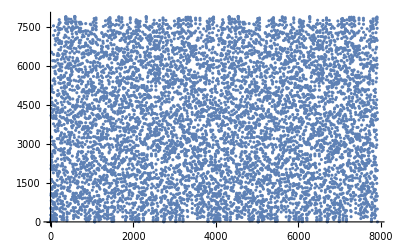

```mathematica
p = Prime[1000]
l = PowerMod[2,Range[1,p-1],p]
ListPlot[l]
```

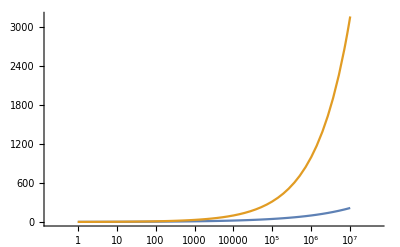

1000000000000

```mathematica
LogLinearPlot[{n^(1/3), n^(1/2)}, {n,1,10000000}, PlotRange->All]
```